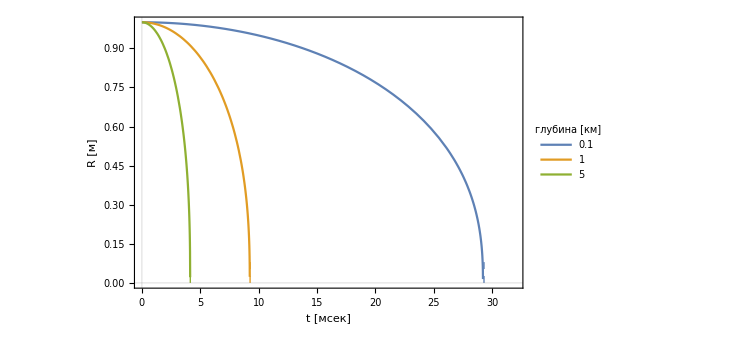

```mathematica
Clear["Global`*"]
tmax=32;
γ=1;
g=9.8;
sol[d_]:=With[{
p=g*d},
NDSolve[{
R''[t]R[t]+1.5 R'[t]^2+p==0,
R[0]==1,
R'[0]==0
},
R,{t,0,tmax/1000},
WorkingPrecision->32, MaxSteps->10^4
]//Quiet
];
depths={0.1, 1,5};
times=Table[√1000/√(γ g d),{d,depths}];
Show[
Plot[
Evaluate[
Table[
R[t/1000]/.First[sol[1000d]],
{d,depths}
]
],
{t,0,tmax},
PlotLegends->Placed[
LineLegend[depths,LegendLabel->"глубина [км]"],
{Right,Top}
],
PlotTheme->"Scientific",
LabelStyle->Directive[FontFamily->"Verdana"],
FrameLabel->{"t [мсек]","R [м]"},
FrameStyle->Directive[16],
FrameTicksStyle->12,
PlotStyle->ColorData[97,"ColorList"]
],
Graphics[
Flatten[
Table[{
ColorData[97,i],Dashed,Line[{{times[[i]]/1.09,0},{times[[i]]/1.09,0.1}}]
},{i,Length[times]}]
]
]
]
```

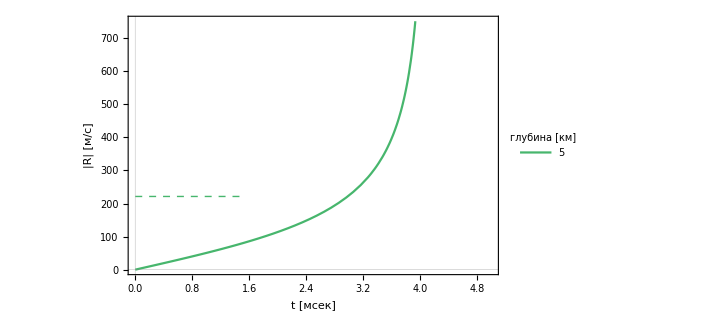

```mathematica
Clear["Global`*"]
tmax=5;
γ=1;
g=9.8;
sol[d_]:=With[{
p=g*d},
NDSolve[{
R''[t]R[t]+1.5 R'[t]^2+p==0,
R[0]==1,
R'[0]==0
},
R,{t,0,tmax/1000},
WorkingPrecision->32, MaxSteps->10^4
]//Quiet
];
depths={5};
csounds=Table[√(γ g d 1000),{d,depths}];
Show[
Plot[
Evaluate[
Table[
-R'[t/1000]/.First[sol[1000d]],
{d,depths}
]
],
{t,0,tmax},
PlotLegends->Placed[
LineLegend[depths,LegendLabel->"глубина [км]"],
{Right,Top}
],
PlotTheme->"Scientific",
LabelStyle->Directive[FontFamily->"Verdana"],
FrameLabel->{"t [мсек]","|Ṙ| [м/с]"},
FrameStyle->Directive[16],
FrameTicksStyle->12,
PlotStyle->ColorData[97,"ColorList"]
],
Graphics[
Flatten[
Table[{
ColorData[97,"ColorList"],Dashed,Line[{{0,csounds[[i]]},{1.5,csounds[[i]]}}]
},{i,Length[csounds]}]
]
]
]
```

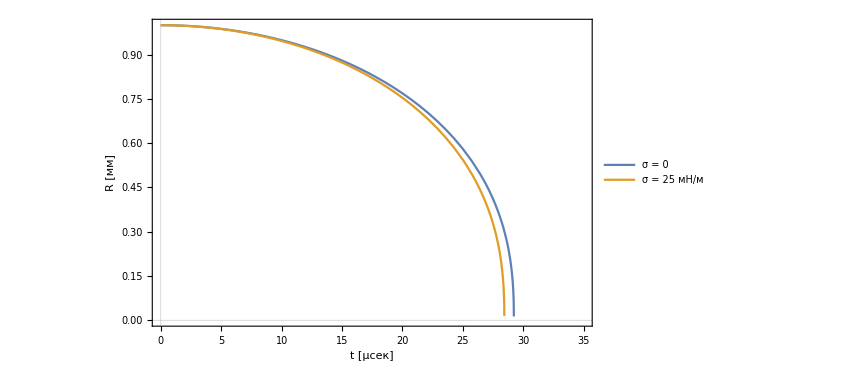

```mathematica
Clear["Global`*"]
tmax=35;
γ=1;
g=9.8;
σ= 25 10^-3;
R0=10^-3;
sol1[d_]:=With[{
p=g*d},
NDSolve[{
R''[t]R[t]+1.5 R'[t]^2+p==0,
R[0]==R0,
R'[0]==0
},
R,{t,0,tmax/10^6},
WorkingPrecision->32, MaxSteps->10^4
]//Quiet
];
sol2[d_]:=With[{
p=g*d},
NDSolve[{
R''[t]R[t]+1.5 R'[t]^2+p+2 σ/R[t]==0,
R[0]==R0,
R'[0]==0
},
R,{t,0,tmax/10^6},
WorkingPrecision->32, MaxSteps->10^4
]//Quiet
];
depths={0.1};
Show[
Plot[
Evaluate[
Table[
{
10^3 R[t/10^6]/.First[sol1[10^3 d]],
10^3 R[t/10^6]/.First[sol2[10^3 d]]
},
{d,depths}
]
],
{t,0,tmax},
PlotLegends->Placed[
LineLegend[{"σ = 0", "σ = 25 :043c:041d/:043c"}],
{Right,Top}
],
PlotTheme->"Scientific",
LabelStyle->Directive[FontFamily->"Verdana"],
FrameLabel->{"t [μсек]","R [мм]"},
FrameStyle->Directive[16],
FrameTicksStyle->12,
PlotStyle->ColorData[97,"ColorList"]
]
]
```

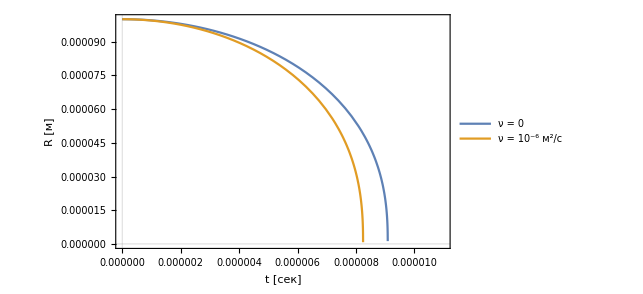

```mathematica
Clear["Global`*"]
tmax=1.1 10^-5;
R0=100 10^-6;
ν=10^-2;
ρW=1000;
σ=  10^-3;
p=101325;
μW=1.002 10^-3;
sol1=
NDSolve[{
R''[t]R[t]+1.5 R'[t]^2+p/ρW==0,
R[0]==R0,
R'[0]==0
},
R,{t,0,1.5 tmax},
WorkingPrecision->32, MaxSteps->10^4
]//Quiet;
sol2=
NDSolve[{
R''[t]R[t]+1.5 R'[t]^2+p/ρW+(2σ)/R[t]+4 μW/ρW R'[t]/R[t]==0,
R[0]==R0,
R'[0]==0
},
R,{t,0,1.5 tmax},
WorkingPrecision->32, MaxSteps->10^4
]//Quiet;
Show[
Plot[{
R[t]/.First[sol1],
R[t]/.First[sol2]
},
{t,0,tmax},
PlotLegends->Placed[
LineLegend[{"ν = 0", "ν = 10^-6 (:043c)^2/:0441"}],
{Right,Top}
],
PlotTheme->"Scientific",
LabelStyle->Directive[FontFamily->"Verdana"],
FrameLabel->{"t [сек]","R [м]"},
FrameStyle->Directive[16],
FrameTicksStyle->12,
PlotStyle->ColorData[97,"ColorList"]
]
]
```

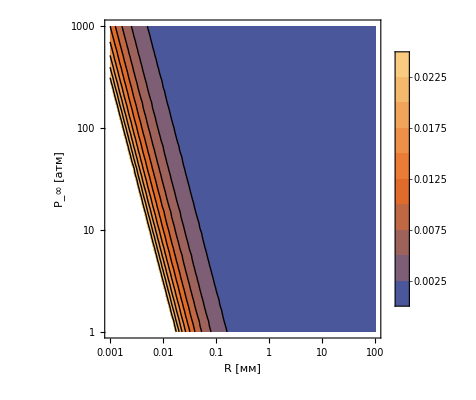

```mathematica
Clear["Global`*"];
P=101325kg m /s^2/m^2;
ν=10^-6 m^2/s;
ρ=1000kg/m^3;
R=10^-3 m;

coeff=Simplify[(4ν)/(R √(P/ρ)),m>0&&s>0&&kg>0];
ContourPlot[
coeff/(r √p),{r,10^-3,100},{p,1,10^3},
PlotTheme->"Scientific",
ScalingFunctions->{"Log","Log"},
PlotLegends->Automatic,
LabelStyle->Directive[FontFamily->"Verdana"],
FrameLabel->{"R [мм]","P_∞ [атм]"},
FrameStyle->Directive[16],
FrameTicksStyle->12,
ScalingFunctions->{Log10[#]&,InverseFunction[Log10[#]&]}
]
```